```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
GreedyAlgorithmFromCost[Cost_]:=((* 入力として枝のコストを与えられたときのGreedyアルゴリズムによる解法 *)
SortList=Ordering[Cost//N];(* 昇順 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
If[Length[VertexList[FindCycle[UndirectedGraph[AppendEdgeProcess]][[1]]]]==Length[Pin],EdgeSolution=AppendEdgeProcess]
]
]
];
EdgeSolution=FindCycle[UndirectedGraph[EdgeSolution]][[1]];
VertexSolution={1};
For[j=1,Length[VertexSolution]≠ Length[EdgeSolution],j++,
VertexSolution=Append[VertexSolution,EdgeSolution[[FirstPosition[EdgeSolution,VertexSolution[[j]]<->_][[1]],2]]]
];
VertexSolution=Append[VertexSolution,1]
)
```

```mathematica
PDSort=Ordering[PD//N](* 昇順 *)
```

{1265,769,700,413,679,530,31,301,638,1140,1002,412,476,583,1138,482,639,1048,1116,21,227,529,794,347,631,818,401,1177,160,161,453,1195,116,190,839,379,999,26,534,743,238,980,393,64,707,770,996,282,397,77,261,823,201,352,369,434,658,667,710,894,994,1099,562,870,1269,124,500,1261,443,460,1104,131,520,650,788,846,955,1063,490,1064,248,576,1232,1248,59,70,768,582,200,257,304,721,1043,1196,226,326,80,285,611,7,627,850,68,235,321,373,495,663,1053,1273,10,132,343,437,1210,118,1180,1,47,198,916,155,795,180,374,349,849,889,1091,1221,546,972,184,384,280,678,1192,50,98,471,1178,45,258,1110,1137,286,348,501,898,240,681,199,302,456,493,521,705,539,540,86,204,252,494,69,162,206,747,187,661,845,156,781,236,442,659,1052,51,1027,281,581,819,1028,872,438,515,127,344,419,1101,1197,1272,466,185,510,952,221,1126,27,392,636,742,57,205,449,1175,605,241,1211,259,787,873,5,454,498,709,780,995,1115,643,30,1179,266,527,1207,125,1182,772,866,194,682,714,921,239,353,473,532,737,1262,168,189,708,649,1250,157,1233,233,242,246,704,609,1120,1127,1184,219,847,535,606,827,1031,1171,1082,1108,15,733,844,37,25,158,651,76,585,946,561,75,441,83,395,1100,2,491,402,641,1006,1263,94,838,305,723,986,82,234,420,465,675,1007,1025,1223,1103,1258,604,951,1193,148,715,216,864,1102,478,1203,869,1047,11,19,222,309,409,853,824,1023,53,97,99,149,375,632,720,765,809,871,104,568,223,940,1226,474,28,481,497,22,292,712,1003,1029,701,1019,1274,245,260,448,415,563,1244,372,492,680,897,538,979,4,56,740,856,1208,1252,900,967,1042,1235,775,791,1174,464,128,6,400,416,790,499,112,1266,367,633,696,976,1066,414,601,656,950,207,613,256,46,79,277,378,640,738,1267,528,744,461,332,425,78,396,531,719,421,892,1249,1264,117,170,525,664,854,877,8,49,228,575,1000,821,84,868,1185,624,878,956,728,96,251,508,645,1090,60,947,188,899,183,688,811,1113,1190,1254,945,1109,210,924,107,345,599,926,690,122,793,218,195,383,533,612,695,1059,300,459,753,1069,1191,524,797,385,841,1070,472,635,364,942,985,1256,450,502,773,1275,462,920,306,341,590,48,329,408,1087,1051,181,893,1213,154,390,516,1154,272,175,997,13,20,303,380,496,565,668,310,410,825,211,545,558,828,123,247,265,146,919,34,271,505,513,1105,657,1039,17,231,335,666,1046,703,433,1172,977,54,58,192,734,975,436,451,998,595,1194,324,1183,455,407,475,144,676,167,488,1060,786,874,1121,23,644,1202,577,74,1044,237,506,572,95,1088,191,970,736,867,1134,610,936,991,337,1024,262,479,134,1085,1224,1255,1022,296,333,458,517,584,1123,626,665,1017,835,628,865,36,350,359,567,677,1080,1118,203,1058,507,1230,176,467,368,905,33,852,16,646,1065,470,105,356,789,1125,1234,3,35,483,1225,489,166,477,693,941,808,1239,1260,512,1173,153,745,805,817,1268,250,662,398,785,660,1139,741,1133,85,208,779,1259,275,446,142,325,931,1097,711,840,939,1009,807,339,713,774,1117,130,536,1077,602,810,1237,943,147,621,816,504,634,29,230,1021,152,209,357,522,1142,1169,1216,702,992,283,1032,24,761,197,278,600,739,289,1061,580,674,904,596,1041,1181,544,346,71,214,548,1089,848,1122,9,243,290,65,673,1253,42,431,1214,842,249,982,718,1188,1247,687,411,55,253,1072,381,480,978,103,914,469,391,159,983,102,202,371,959,573,87,697,63,1270,468,686,66,822,330,1132,1271,647,14,960,1098,1135,101,422,569,826,925,971,1124,212,1204,145,509,1049,284,619,722,855,884,119,598,1040,1112,503,523,615,1030,589,655,820,1242,1086,342,953,989,276,511,52,263,729,426,150,217,566,685,1084,486,1092,126,424,514,962,1096,151,193,254,399,43,62,861,1153,1243,1152,165,173,370,1205,777,901,937,1014,108,1209,836,1200,910,1150,1005,1157,883,405,607,213,423,623,766,1081,755,92,394,564,990,993,81,220,553,984,338,746,837,752,1020,1018,1187,652,834,1155,1228,316,224,244,1095,586,684,692,843,291,1026,485,358,574,215,196,93,298,457,463,1094,1251,887,1167,182,642,911,1056,186,1227,377,782,72,279,727,445,1111,295,526,559,806,981,255,294,760,616,726,177,355,12,143,603,833,44,264,1136,948,1220,1050,268,229,974,1083,1038,944,169,1215,1001,452,724,32,875,106,389,38,798,917,570,930,1165,895,386,1068,1037,1062,73,439,487,815,307,315,554,725,1168,776,862,382,796,518,671,172,987,1170,915,730,269,274,751,40,351,1238,890,608,418,267,896,41,164,404,313,689,654,973,1236,334,225,388,857,653,120,618,331,617,110,735,18,717,767,287,683,913,1130,417,927,174,336,961,1008,314,587,881,91,133,319,706,922,432,591,114,327,691,328,614,1045,139,171,365,694,863,758,1257,429,716,851,888,1071,1222,270,376,578,387,90,648,932,113,1143,1151,547,1218,670,444,588,812,882,232,958,988,163,519,543,949,1055,1199,778,792,783,1186,1189,440,135,537,299,362,1119,100,273,322,592,1176,435,579,61,297,902,1229,427,923,89,111,293,803,1141,67,484,880,859,804,954,622,860,876,771,1093,121,928,762,831,886,929,340,918,672,891,802,571,1206,366,750,430,620,1217,363,428,625,551,1035,1166,968,320,698,312,1129,1015,140,629,965,784,288,731,354,1158,403,597,593,933,129,552,1010,1078,308,360,1198,560,813,1240,908,814,1036,1106,141,879,903,178,39,1245,406,907,1156,1231,555,549,906,754,938,749,757,1054,1147,1004,637,1016,1034,323,909,1148,830,594,1246,550,1149,1212,1162,318,966,1073,699,732,1075,669,1079,969,542,630,1067,1219,1012,801,885,311,934,179,759,957,109,832,1013,1076,1107,88,541,361,756,963,1128,138,800,748,447,858,912,137,1163,1164,317,1241,935,1131,115,1057,964,1146,829,1033,1114,556,1145,763,1074,1011,1161,557,1201,799,1160,136,764,1144,1159}

```mathematica
EdgeSolution={};
EdgeProcess={Ruleg[[PDSort[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[PDSort[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
If[Length[VertexList[AppendEdgeProcess]]==Length[Pin],EdgeSolution=AppendEdgeProcess]
]
]
]
EdgeSolution=FindCycle[UndirectedGraph[EdgeSolution]][[1]]
```

{46<->12,12<->47,47<->18,18<->4,4<->17,17<->37,37<->44,44<->15,15<->45,45<->33,33<->39,39<->10,10<->49,49<->9,9<->50,50<->16,16<->2,2<->29,29<->21,21<->34,34<->30,30<->5,5<->38,38<->11,11<->32,32<->1,1<->22,22<->36,36<->35,35<->20,20<->3,3<->28,28<->31,31<->8,8<->26,26<->7,7<->23,23<->24,24<->43,43<->40,40<->42,42<->19,19<->41,41<->13,13<->25,25<->14,14<->6,6<->48,48<->27,27<->51,51<->46}

```mathematica
VertexSolution={1};
For[j=1,Length[VertexSolution]≠ Length[EdgeSolution],j++,
VertexSolution=Append[VertexSolution,EdgeSolution[[FirstPosition[EdgeSolution,VertexSolution[[j]]<->_][[1]],2]]]
];
VertexSolution=Append[VertexSolution,1]
```

{1,22,36,35,20,3,28,31,8,26,7,23,24,43,40,42,19,41,13,25,14,6,48,27,51,46,12,47,18,4,17,37,44,15,45,33,39,10,49,9,50,16,2,29,21,34,30,5,38,11,32,1}

### 渦電流の計算

```mathematica
Pin={{0,0},{1,2},{1.5,0.5},{3,0.7},{3.5,3.3},{5,0}}(*Point input*)
```

{{0,0},{1,2},{1.5,0.5},{3,0.7},{3.5,3.3},{5,0}}

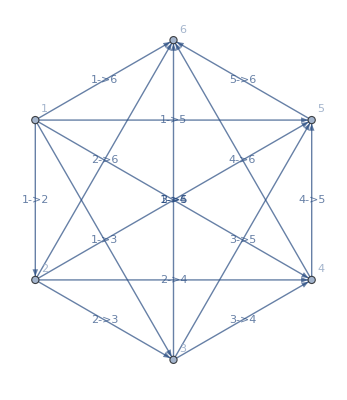

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"]
```

```mathematica
h=LoopMatrix[Gin]
```

{{0,0,0,1,-1,0,0,0,0,0,0,0,0,0,1},{0,0,1,0,-1,0,0,0,0,0,0,0,0,1,0},{0,0,1,-1,0,0,0,0,0,0,0,0,1,0,0},{0,1,0,0,-1,0,0,0,0,0,0,1,0,0,0},{0,1,0,-1,0,0,0,0,0,0,1,0,0,0,0},{0,1,-1,0,0,0,0,0,0,1,0,0,0,0,0},{1,0,0,0,-1,0,0,0,1,0,0,0,0,0,0},{1,0,0,-1,0,0,0,1,0,0,0,0,0,0,0},{1,0,-1,0,0,0,1,0,0,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0,0,0,0,0}}

```mathematica
Ruleg
```

{1→2,1→3,1→4,1→5,1→6,2→3,2→4,2→5,2→6,3→4,3→5,3→6,4→5,4→6,5→6}

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}](* Point Distance *)
```

{√5,1.58114,3.08058,4.81041,5,1.58114,2.38537,2.8178,2 √5,1.51327,3.44093,3.53553,2.64764,2.11896,3.62491}

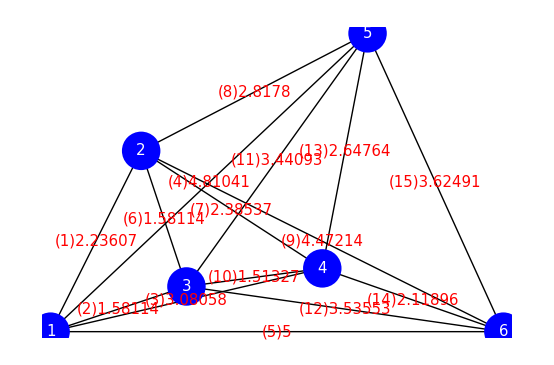

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[PD[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```

```mathematica
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD
```

{{√5,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,1.58114,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,3.08058,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,4.81041,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,1.58114,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.38537,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.8178,0.,0.,0.,0.,0.,0.,0.},{0,0,0,0,0,0,0,0,2 √5,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.51327,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.44093,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.53553,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.64764,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.11896,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.62491}}

```mathematica
s=Table[0,{i,Length[EdgeRules[Gin]]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}](* Fundamental Loop Point *)
```

{{{5,0},{0,0},{3.5,3.3}},{{5,0},{0,0},{3,0.7}},{{3.5,3.3},{0,0},{3,0.7}},{{5,0},{0,0},{1.5,0.5}},{{3.5,3.3},{0,0},{1.5,0.5}},{{3,0.7},{0,0},{1.5,0.5}},{{5,0},{0,0},{1,2}},{{3.5,3.3},{0,0},{1,2}},{{3,0.7},{0,0},{1,2}},{{1.5,0.5},{0,0},{1,2}}}

```mathematica
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}](* 右回りならば負、左回りならば正 *)
```

{-1,-1,1,-1,1,-1,-1,-1,-1,-1}

```mathematica
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}](* Fundamental Loop Area *)
```

{8.25,1.75,3.725,1.25,1.6,0.225,5,1.85,2.65,1.25}

```mathematica
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}](* 誘導起電力は右回りなら負、左回りなら正 *)
```

{-8.25,-1.75,3.725,-1.25,1.6,-0.225,-5,-1.85,-2.65,-1.25}

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.671869,0.176089,0.298125,-0.385242,0.582897,0.335685,-0.0961094,-0.781044,-0.130401,0.274226,-0.15449,0.392038,0.360106,0.116135,-0.96067}

```mathematica
Reverse[Ordering[Abs[Curr]]]
```

{15,8,1,5,12,4,13,6,3,10,2,11,9,14,7}

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

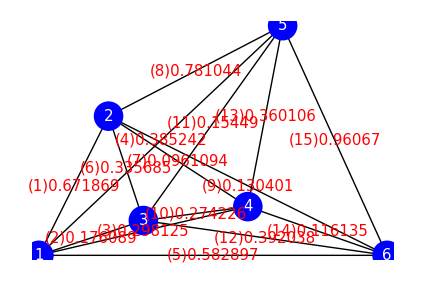

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### TSPの解

```mathematica
Reverse[Ordering[Abs[Curr]]](* 降順 *)
```

{15,8,1,5,12,4,13,6,3,10,2,11,9,14,7}

```mathematica
Reverse[Ordering[PD]](* 誤り *)
```

{9,1,5,4,15,12,11,3,8,13,7,14,6,2,10}

```mathematica
Reverse[Ordering[PD//N]](* 降順 *)
```

{5,4,9,15,12,11,3,8,13,7,1,14,6,2,10}

```mathematica
PDSort=Ordering[PD//N](* 昇順 *)
```

{10,2,6,14,1,7,13,8,3,11,12,15,9,4,5}

```mathematica
PD//N
```

{2.23607,1.58114,3.08058,4.81041,5.,1.58114,2.38537,2.8178,4.47214,1.51327,3.44093,3.53553,2.64764,2.11896,3.62491}

```mathematica
NewCost=Abs[PD/Curr ]
```

{3.32813,8.97922,10.3332,12.4867,8.57784,4.71018,24.8194,3.60774,34.2953,5.51836,22.2728,9.01834,7.35239,18.2456,3.77332}

```mathematica
NewCostSort=Ordering[Abs[PD/Curr]](* 昇順 *)
```

{1,8,15,6,10,13,5,2,12,3,4,14,11,7,9}

```mathematica
Ruleg
```

{1→2,1→3,1→4,1→5,1→6,2→3,2→4,2→5,2→6,3→4,3→5,3→6,4→5,4→6,5→6}

```mathematica
EdgeProcess={Ruleg[[PDSort[[1]]]]}
```

{3→4}

```mathematica
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[PDSort[[2]]]]]
```

{3→4,1→3}

```mathematica
VertexDegree[AppendEdgeProcess]
```

{2,1,1}

```mathematica
Max[VertexDegree[AppendEdgeProcess]]≤2
```

True

```mathematica
AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]]
```

True

```mathematica
EdgeProcess=AppendEdgeProcess
```

{3→4,1→3}

```mathematica
Length[VertexList[EdgeProcess]]<Length[Pin]
```

True

```mathematica
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[PDSort[[3]]]]]
```

{3→4,1→3,2→3}

```mathematica
Max[VertexDegree[AppendEdgeProcess]]≤2
```

False

```mathematica
AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]]
```

True

```mathematica
Length[VertexList[EdgeProcess]]<Length[Pin]
```

True

```mathematica
EdgeSolution={};
EdgeProcess={Ruleg[[PDSort[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[PDSort[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
If[Length[VertexList[FindCycle[UndirectedGraph[AppendEdgeProcess]][[1]]]]==Length[Pin],EdgeSolution=AppendEdgeProcess]
]
]
]
EdgeSolution=FindCycle[UndirectedGraph[EdgeSolution]][[1]]
```

{3<->1,1<->2,2<->5,5<->6,6<->4,4<->3}

```mathematica
VertexSolution={1};
For[j=1,Length[VertexSolution]≠ Length[EdgeSolution],j++,
VertexSolution=Append[VertexSolution,EdgeSolution[[FirstPosition[EdgeSolution,VertexSolution[[j]]<->_][[1]],2]]]
];
VertexSolution=Append[VertexSolution,1]
```

{1,2,5,6,4,3,1}

{13.8922,{1,3,4,6,5,2,1}}

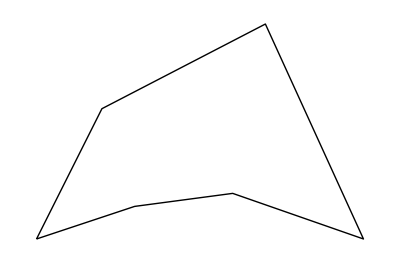

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

```mathematica
GreedyAlgorithmFromCost[PD]
Graphics[Line[Pin[[VertexSolution]]]]
```

{1,2,5,6,4,3,1}

-Graphics-

{1,4,3,6,5,2,1}

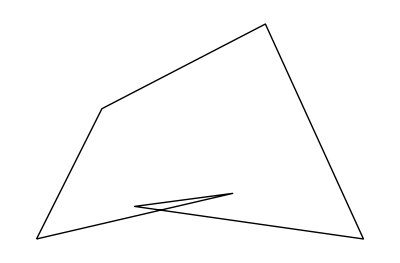

```mathematica
GreedyAlgorithmFromCost[Abs[1/Curr]]
Graphics[Line[Pin[[VertexSolution]]]]
```

```mathematica
GreedyAlgorithmFromCost[Curr](* 正負のあるCurrでなぜ最適解が求められたのかわからない *)
Graphics[Line[Pin[[VertexSolution]]]]
```

{1,3,4,6,5,2,1}

-Graphics-

```mathematica
GreedyAlgorithmFromCost[Abs[PD/Curr]]
Graphics[Line[Pin[[VertexSolution]]]]
```

{1,2,5,6,4,3,1}

-Graphics-

```mathematica
Pin=Drop[Drop[Import["eil51.tsp","Table"],6],-1][[All,2;;3]]
```

{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}}

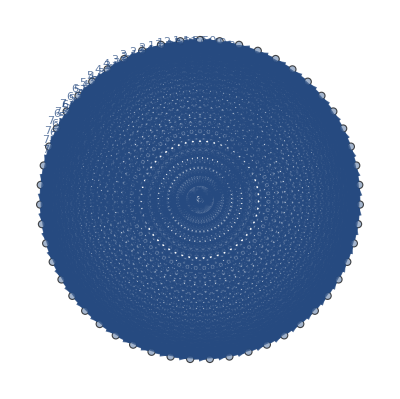

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin]
```

{1}
 |  |  |  |

```mathematica
Ruleg
```

{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,1→11,1→12,1→13,1→14,1→15,1→16,1→17,1→18,1→19,1→20,1→21,1→22,1→23,1→24,1→25,1→26,1→27,1→28,1→29,1→30,1→31,1→32,1→33,1→34,1→35,1→36,1→37,1→38,1→39,1→40,1→41,1→42,1→43,1→44,1→45,1→46,1→47,1→48,1→49,1→50,1→51,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,2→11,2→12,2→13,2→14,2→15,2→16,2→17,2→18,2→19,2→20,2→21,2→22,2→23,2→24,2→25,2→26,2→27,2→28,2→29,2→30,2→31,2→32,2→33,2→34,2→35,2→36,2→37,2→38,2→39,2→40,2→41,2→42,2→43,2→44,2→45,2→46,2→47,2→48,2→49,2→50,2→51,3→4,3→5,3→6,3→7,3→8,3→9,3→10,3→11,3→12,3→13,3→14,3→15,3→16,3→17,3→18,3→19,3→20,3→21,3→22,3→23,3→24,3→25,3→26,3→27,3→28,3→29,3→30,3→31,3→32,3→33,3→34,3→35,3→36,3→37,3→38,3→39,3→40,3→41,3→42,3→43,3→44,3→45,3→46,3→47,3→48,3→49,3→50,3→51,4→5,4→6,4→7,4→8,4→9,4→10,4→11,4→12,4→13,4→14,4→15,4→16,4→17,4→18,4→19,4→20,4→21,4→22,4→23,4→24,4→25,4→26,4→27,4→28,4→29,4→30,4→31,4→32,4→33,4→34,4→35,4→36,4→37,4→38,4→39,4→40,4→41,4→42,4→43,4→44,4→45,4→46,4→47,4→48,4→49,4→50,4→51,5→6,5→7,5→8,5→9,5→10,5→11,5→12,5→13,5→14,5→15,5→16,5→17,5→18,5→19,5→20,5→21,5→22,5→23,5→24,5→25,5→26,5→27,5→28,5→29,5→30,5→31,5→32,5→33,5→34,5→35,5→36,5→37,5→38,5→39,5→40,5→41,5→42,5→43,5→44,5→45,5→46,5→47,5→48,5→49,5→50,5→51,6→7,6→8,6→9,6→10,6→11,6→12,6→13,6→14,6→15,6→16,6→17,6→18,6→19,6→20,6→21,6→22,6→23,6→24,6→25,6→26,6→27,6→28,6→29,6→30,6→31,6→32,6→33,6→34,6→35,6→36,6→37,6→38,6→39,6→40,6→41,6→42,6→43,6→44,6→45,6→46,6→47,6→48,6→49,6→50,6→51,7→8,7→9,7→10,7→11,7→12,7→13,7→14,7→15,7→16,7→17,7→18,7→19,7→20,7→21,7→22,7→23,7→24,7→25,7→26,7→27,7→28,7→29,7→30,7→31,7→32,7→33,7→34,7→35,7→36,7→37,7→38,7→39,7→40,7→41,7→42,7→43,7→44,7→45,7→46,7→47,7→48,7→49,7→50,7→51,8→9,8→10,8→11,8→12,8→13,8→14,8→15,8→16,8→17,8→18,8→19,8→20,8→21,8→22,8→23,8→24,8→25,8→26,8→27,8→28,8→29,8→30,8→31,8→32,8→33,8→34,8→35,8→36,8→37,8→38,8→39,8→40,8→41,8→42,8→43,8→44,8→45,8→46,8→47,8→48,8→49,8→50,8→51,9→10,9→11,9→12,9→13,9→14,9→15,9→16,9→17,9→18,9→19,9→20,9→21,9→22,9→23,9→24,9→25,9→26,9→27,9→28,9→29,9→30,9→31,9→32,9→33,9→34,9→35,9→36,9→37,9→38,9→39,9→40,9→41,9→42,9→43,9→44,9→45,9→46,9→47,9→48,9→49,9→50,9→51,10→11,10→12,10→13,10→14,10→15,10→16,10→17,10→18,10→19,10→20,10→21,10→22,10→23,10→24,10→25,10→26,10→27,10→28,10→29,10→30,10→31,10→32,10→33,10→34,10→35,10→36,10→37,10→38,10→39,10→40,10→41,10→42,10→43,10→44,10→45,10→46,10→47,10→48,10→49,10→50,10→51,11→12,11→13,11→14,11→15,11→16,11→17,11→18,11→19,11→20,11→21,11→22,11→23,11→24,11→25,11→26,11→27,11→28,11→29,11→30,11→31,11→32,11→33,11→34,11→35,11→36,11→37,11→38,11→39,11→40,11→41,11→42,11→43,11→44,11→45,11→46,11→47,11→48,11→49,11→50,11→51,12→13,12→14,12→15,12→16,12→17,12→18,12→19,12→20,12→21,12→22,12→23,12→24,12→25,12→26,12→27,12→28,12→29,12→30,12→31,12→32,12→33,12→34,12→35,12→36,12→37,12→38,12→39,12→40,12→41,12→42,12→43,12→44,12→45,12→46,12→47,12→48,12→49,12→50,12→51,13→14,13→15,13→16,13→17,13→18,13→19,13→20,13→21,13→22,13→23,13→24,13→25,13→26,13→27,13→28,13→29,13→30,13→31,13→32,13→33,13→34,13→35,13→36,13→37,13→38,13→39,13→40,13→41,13→42,13→43,13→44,13→45,13→46,13→47,13→48,13→49,13→50,13→51,14→15,14→16,14→17,14→18,14→19,14→20,14→21,14→22,14→23,14→24,14→25,14→26,14→27,14→28,14→29,14→30,14→31,14→32,14→33,14→34,14→35,14→36,14→37,14→38,14→39,14→40,14→41,14→42,14→43,14→44,14→45,14→46,14→47,14→48,14→49,14→50,14→51,15→16,15→17,15→18,15→19,15→20,15→21,15→22,15→23,15→24,15→25,15→26,15→27,15→28,15→29,15→30,15→31,15→32,15→33,15→34,15→35,15→36,15→37,15→38,15→39,15→40,15→41,15→42,15→43,15→44,15→45,15→46,15→47,15→48,15→49,15→50,15→51,16→17,16→18,16→19,16→20,16→21,16→22,16→23,16→24,16→25,16→26,16→27,16→28,16→29,16→30,16→31,16→32,16→33,16→34,16→35,16→36,16→37,16→38,16→39,16→40,16→41,16→42,16→43,16→44,16→45,16→46,16→47,16→48,16→49,16→50,16→51,17→18,17→19,17→20,17→21,17→22,17→23,17→24,17→25,17→26,17→27,17→28,17→29,17→30,17→31,17→32,17→33,17→34,17→35,17→36,17→37,17→38,17→39,17→40,17→41,17→42,17→43,17→44,17→45,17→46,17→47,17→48,17→49,17→50,17→51,18→19,18→20,18→21,18→22,18→23,18→24,18→25,18→26,18→27,18→28,18→29,18→30,18→31,18→32,18→33,18→34,18→35,18→36,18→37,18→38,18→39,18→40,18→41,18→42,18→43,18→44,18→45,18→46,18→47,18→48,18→49,18→50,18→51,19→20,19→21,19→22,19→23,19→24,19→25,19→26,19→27,19→28,19→29,19→30,19→31,19→32,19→33,19→34,19→35,19→36,19→37,19→38,19→39,19→40,19→41,19→42,19→43,19→44,19→45,19→46,19→47,19→48,19→49,19→50,19→51,20→21,20→22,20→23,20→24,20→25,20→26,20→27,20→28,20→29,20→30,20→31,20→32,20→33,20→34,20→35,20→36,20→37,20→38,20→39,20→40,20→41,20→42,20→43,20→44,20→45,20→46,20→47,20→48,20→49,20→50,20→51,21→22,21→23,21→24,21→25,21→26,21→27,21→28,21→29,21→30,21→31,21→32,21→33,21→34,21→35,21→36,21→37,21→38,21→39,21→40,21→41,21→42,21→43,21→44,21→45,21→46,21→47,21→48,21→49,21→50,21→51,22→23,22→24,22→25,22→26,22→27,22→28,22→29,22→30,22→31,22→32,22→33,22→34,22→35,22→36,22→37,22→38,22→39,22→40,22→41,22→42,22→43,22→44,22→45,22→46,22→47,22→48,22→49,22→50,22→51,23→24,23→25,23→26,23→27,23→28,23→29,23→30,23→31,23→32,23→33,23→34,23→35,23→36,23→37,23→38,23→39,23→40,23→41,23→42,23→43,23→44,23→45,23→46,23→47,23→48,23→49,23→50,23→51,24→25,24→26,24→27,24→28,24→29,24→30,24→31,24→32,24→33,24→34,24→35,24→36,24→37,24→38,24→39,24→40,24→41,24→42,24→43,24→44,24→45,24→46,24→47,24→48,24→49,24→50,24→51,25→26,25→27,25→28,25→29,25→30,25→31,25→32,25→33,25→34,25→35,25→36,25→37,25→38,25→39,25→40,25→41,25→42,25→43,25→44,25→45,25→46,25→47,25→48,25→49,25→50,25→51,26→27,26→28,26→29,26→30,26→31,26→32,26→33,26→34,26→35,26→36,26→37,26→38,26→39,26→40,26→41,26→42,26→43,26→44,26→45,26→46,26→47,26→48,26→49,26→50,26→51,27→28,27→29,27→30,27→31,27→32,27→33,27→34,27→35,27→36,27→37,27→38,27→39,27→40,27→41,27→42,27→43,27→44,27→45,27→46,27→47,27→48,27→49,27→50,27→51,28→29,28→30,28→31,28→32,28→33,28→34,28→35,28→36,28→37,28→38,28→39,28→40,28→41,28→42,28→43,28→44,28→45,28→46,28→47,28→48,28→49,28→50,28→51,29→30,29→31,29→32,29→33,29→34,29→35,29→36,29→37,29→38,29→39,29→40,29→41,29→42,29→43,29→44,29→45,29→46,29→47,29→48,29→49,29→50,29→51,30→31,30→32,30→33,30→34,30→35,30→36,30→37,30→38,30→39,30→40,30→41,30→42,30→43,30→44,30→45,30→46,30→47,30→48,30→49,30→50,30→51,31→32,31→33,31→34,31→35,31→36,31→37,31→38,31→39,31→40,31→41,31→42,31→43,31→44,31→45,31→46,31→47,31→48,31→49,31→50,31→51,32→33,32→34,32→35,32→36,32→37,32→38,32→39,32→40,32→41,32→42,32→43,32→44,32→45,32→46,32→47,32→48,32→49,32→50,32→51,33→34,33→35,33→36,33→37,33→38,33→39,33→40,33→41,33→42,33→43,33→44,33→45,33→46,33→47,33→48,33→49,33→50,33→51,34→35,34→36,34→37,34→38,34→39,34→40,34→41,34→42,34→43,34→44,34→45,34→46,34→47,34→48,34→49,34→50,34→51,35→36,35→37,35→38,35→39,35→40,35→41,35→42,35→43,35→44,35→45,35→46,35→47,35→48,35→49,35→50,35→51,36→37,36→38,36→39,36→40,36→41,36→42,36→43,36→44,36→45,36→46,36→47,36→48,36→49,36→50,36→51,37→38,37→39,37→40,37→41,37→42,37→43,37→44,37→45,37→46,37→47,37→48,37→49,37→50,37→51,38→39,38→40,38→41,38→42,38→43,38→44,38→45,38→46,38→47,38→48,38→49,38→50,38→51,39→40,39→41,39→42,39→43,39→44,39→45,39→46,39→47,39→48,39→49,39→50,39→51,40→41,40→42,40→43,40→44,40→45,40→46,40→47,40→48,40→49,40→50,40→51,41→42,41→43,41→44,41→45,41→46,41→47,41→48,41→49,41→50,41→51,42→43,42→44,42→45,42→46,42→47,42→48,42→49,42→50,42→51,43→44,43→45,43→46,43→47,43→48,43→49,43→50,43→51,44→45,44→46,44→47,44→48,44→49,44→50,44→51,45→46,45→47,45→48,45→49,45→50,45→51,46→47,46→48,46→49,46→50,46→51,47→48,47→49,47→50,47→51,48→49,48→50,48→51,49→50,49→51,50→51}

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}](* Point Distance *)
```

{3 √17,3 √41,√965,√493,√281,√521,2 √34,√586,√1157,√146,2 √109,√1753,5 √29,√1297,√346,√941,√761,3 √233,2 √109,5 √29,5 √2,√466,29,2 √274,2 √89,√65,3 √29,√457,√1066,17,√37,3 √205,√937,√746,√965,5 √37,√353,√1853,2 √785,√1954,2 √505,4 √73,√1418,2 √442,√194,4 √34,3 √17,√697,√586,√193,3 √26,√1370,√442,2 √197,2 √305,√493,√265,2 √197,√113,√613,4 √157,√1418,√1258,√73,2 √290,16 √5,36 √2,√145,√218,√113,√1153,13 √10,√1885,13 √5,√362,6 √10,√82,√565,4 √34,√130,3 √170,20,√365,2 √149,√1018,2 √53,2 √314,√3785,√2545,√2305,√2161,√1517,√1621,√389,√865,6 √17,√442,√193,√442,2 √617,10 √13,25 √2,√1226,√445,31,5 √74,√629,√1465,√3730,2 √521,16 √10,23,√2306,√2186,3 √458,√61,2 √146,√149,√1345,4 √130,√2701,√641,2 √185,3 √10,2 √73,√1405,5 √10,2 √130,6 √82,√1042,√101,√146,2 √541,√890,35 √2,√5573,√3973,√3877,47,√2885,√3085,5 √41,√1753,9 √10,4 √82,√745,2 √265,4 √26,√442,√1378,√1417,√1073,√986,√709,√157,√226,8 √5,2 √89,√1249,√58,√58,√218,√2393,2 √505,17 √5,√977,2 √205,√313,7 √37,2 √146,√2210,2 √482,17 √5,√2138,2 √181,2 √233,√1730,√3133,43 √2,4 √10,√706,√1642,25,√181,√257,√1669,√221,√617,√313,√61,√866,2 √197,√1417,2 √74,5 √26,√1618,√1105,3 √17,√202,5 √5,√85,25 √2,4 √58,2 √53,√265,√218,√538,√1018,√1073,2 √157,√733,3 √145,2 √377,√1153,√1613,2 √106,√1378,18 √2,3 √37,3 √170,2 √65,2 √109,15 √2,11 √13,5 √82,8 √2,5 √2,√586,√1801,√1069,√761,√2381,5 √13,√401,√145,√229,5 √34,2 √17,√305,10 √2,4 √17,5 √13,√1157,2 √394,3 √53,5 √13,2 √185,√106,√1186,√997,6 √17,2 √53,2 √305,√1417,√1706,√541,5 √5,√194,√277,3 √53,√82,2 √221,√1370,√1769,2 √185,√290,√1994,2 √449,√1937,2 √562,√746,12 √5,2 √617,√1937,√1021,37,√545,√1105,√1693,√185,√241,4 √5,√1090,5 √53,√130,√197,5 √85,2 √730,√1109,√1157,2 √397,√466,√2570,√1709,10 √17,30,2 √629,5 √65,3 √274,√661,√37,√202,5 √29,5 √5,√394,2 √173,√1906,√2977,2 √109,√730,5 √146,2 √709,45,2 √538,√1906,28 √2,6 √113,3 √377,√2165,5 √113,√145,√2473,√3293,3 √89,5 √41,8 √2,√2186,13 √13,√698,√1282,√2081,√562,30,√2045,√761,√2141,21 √2,√1537,√1037,5 √109,2 √173,√1361,√146,5 √10,√629,24 √2,2 √13,√197,13,5 √37,√1954,√85,√305,√2929,√1741,√962,√1073,√1601,5 √37,√2993,2 √953,3 √274,2 √701,2 √170,√2210,4 √173,√530,6 √26,√85,17 √5,25 √2,√485,√145,2 √41,√442,√2273,41,√545,8,5 √29,35,√1921,5 √26,√181,26,12 √13,√2297,5 √82,5 √74,√709,√1237,3 √29,6 √2,39,√365,√565,9,10 √10,√1417,√521,√53,√373,√2938,2 √505,√1490,√3170,2 √202,√698,2 √109,√730,√1213,√41,4 √2,√533,√481,√521,2 √533,3 √218,5 √10,√401,2 √145,10 √13,2 √377,√1405,√562,9 √17,√2521,√2810,5 √89,√2785,3 √130,2 √545,√778,√85,50,√794,√146,2 √61,√1885,12 √17,√362,2 √58,10,√2341,√1697,√1021,√3965,3 √53,√265,√685,√797,2 √458,√58,√281,√802,√202,5 √65,√901,√661,10,3 √61,√689,5 √65,√514,√401,16,2 √233,√1277,√1234,3 √106,√193,√677,√305,2 √113,√809,√41,√977,5 √17,2 √221,35,√461,3 √5,√965,√2594,40,√1402,√1898,2 √205,√970,2 √26,√370,√485,√205,2 √53,√145,5 √29,√461,√281,3 √58,√97,√197,√685,26 √2,√1061,√746,5 √34,√929,6 √17,4 √82,√257,37,√985,√754,√1405,7 √5,√709,√901,31 √2,√2393,√101,√205,√1073,26 √2,3 √74,2 √146,10 √17,√290,2 √137,5 √2,6,√565,√305,5 √26,√65,13 √2,√1042,√2465,2 √122,4 √13,4 √13,√3793,√3538,√2393,√1145,3 √82,√173,√2333,√1154,2 √802,√3338,√2813,4 √185,3 √170,√1906,40 √2,19 √13,10 √53,3 √82,10 √17,2 √754,19,√89,√481,39,5 √29,√1381,5 √37,√449,10 √13,√1858,3 √305,5 √34,2 √313,√1601,√586,√106,√842,√2281,50,15 √5,√241,2 √29,√41,√901,6 √10,√1586,2 √538,√2341,√1354,2 √173,2 √545,√2482,√2941,3 √370,20 √2,√1138,√2938,√1345,√629,√1105,√533,9 √13,√1753,√409,√269,13 √2,2 √373,√1961,2 √82,√881,√130,5 √26,√538,21 √5,26 √2,√1717,√2081,4 √130,5 √53,√2785,2 √265,5 √106,2 √377,11 √5,√2810,2 √226,2 √34,√914,√2885,√3538,2 √13,√442,√530,√1061,√677,3 √29,√3265,√37,3 √5,√545,√377,√1642,12 √2,29,6 √17,√949,√1289,√2305,√314,√101,2 √89,4 √97,11 √17,3 √226,√1354,√533,√757,√85,2 √58,√1009,√221,√997,√145,2 √146,√905,√761,√85,5 √29,√3434,6 √65,31 √2,37 √2,2 √290,√1130,2 √101,9 √10,5 √37,√185,4 √2,√485,10 √2,2 √74,5 √85,√1586,√1381,√1277,√1202,25,45,√634,4 √137,√1586,√977,2 √554,5 √26,√530,2 √314,5 √113,2 √853,√26,6 √13,8 √17,√773,5 √13,√205,√2165,√73,√313,√281,√85,2 √257,√466,√1037,√298,4 √26,5 √89,9 √26,√1201,√577,√442,5 √5,5 √53,√394,2 √458,√1906,√1717,4 √106,√610,√1370,44,15 √13,2 √853,√346,2 √197,6 √58,3 √97,√305,√545,√1105,√493,√1013,3 √29,√65,2 √137,√986,√1537,√218,√3961,√3242,√2777,√1945,√1546,√661,√3221,√1514,6 √106,5 √130,√2221,8 √58,√1714,3 √122,52,13 √29,2 √1409,√442,2 √377,2 √530,√113,5,√73,√2665,√293,√685,√1037,√505,6 √53,5 √58,5 √97,√1018,√281,√226,29 √2,√2437,10 √29,10 √10,√829,√277,√101,√962,√521,√505,5 √97,√641,5 √2,√157,√1921,√673,√1853,52 √2,√3890,60,2 √685,√2578,6 √73,√986,10 √17,√1033,3 √109,√442,9 √13,25,√2341,2 √754,√3041,√1901,2 √265,√986,2 √13,√241,√1354,4 √37,16 √5,√82,21,√730,10 √13,13 √2,3 √82,3 √505,√3329,√2705,√3733,√1753,√1553,3 √101,√1469,√1538,14 √2,√61,2 √257,26,√1181,√1586,√346,15,√101,√337,34,13,√137,5 √89,√937,2 √109,3 √65,5 √53,√493,√2053,√3970,8 √41,5 √106,√1418,6 √53,√2218,2 √106,√914,√293,√877,2 √149,√433,√89,√442,11 √2,√277,√829,3 √205,6 √74,3 √65,11 √5,√3109,51,2 √538,√2353,√1481,5 √53,√3613,√2722,2 √409,√2234,√170,14 √10,37 √2,2 √145,√706,√85,√1865,20 √5,√485,√197,√617,10 √5,5 √58,2 √629,25 √5,√1130,6 √26,2 √802,√3170,√3037,√3314,6 √41,√1658,√3970,5 √85,√1229,√1933,3 √17,√1853,5 √109,√745,√689,√298,8 √34,3 √281,2 √157,10 √13,√629,√2137,√2701,√2722,√1861,5 √41,√2305,√2941,5 √146,√4097,√881,√1453,√3233,2 √257,15 √2,14 √5,2 √170,23 √2,4 √113,√626,6 √10,√613,√1781,√2402,√533,√409,√257,√1361,√2642,√101,11 √5,5 √149,√2381,25 √2,√1297,√2141,3 √157,√3833,2 √1082,17 √10,10 √34,10 √5,√2818,2 √877,√866,10 √13,√173,√2041,√1802,√793,√530,28,35,7 √10,2 √17,10 √17,√1186,√1249,3 √170,2 √170,√394,√1930,√2389,√1361,5 √61,√881,33,5 √61,√85,√281,√74,2 √181,√797,8,√586,5 √73,2 √10,√466,3 √362,2 √370,√377,2 √101,√2146,2 √257,4 √185,√5165,√3589,√3733,√1453,13 √17,√3265,√905,√1549,6 √13,√1546,√1069,√898,21,21 √2,2 √101,2 √397,3 √26,√241,√466,26 √2,13 √2,√1090,√4573,√3265,√2813,√3065,√1873,19 √5,√757,√1345,√1138,10 √5,5 √5,4 √53,21 √5,√761,√433,3 √5,4 √82,√1789,√701,√233,√145,5 √130,2 √601,√1658,√4178,4 √58,5 √26,2 √205,√1114,√1873,√101,2 √26,√953,√530,√3562,12 √13,√661,26,√2234,2 √305,10 √34,√4993,√3433,√3737,√1049,√2965,√3485,5 √37,√1513,2 √85,√1802,√1385,√890,4 √85,√698,√865,√1154,6 √17,√170,√1402,√2689,5 √65,√1585,3 √157,5 √41,√1297,√85,√365,5 √10,2 √106,9 √5,10,√754,√3065,√3770,2 √85,√626,√194,√1697,√1345,25,√4597,√281,7,√1037,5 √37,3 √274,2 √82,√829,34,√901,10 √13,√962,2 √65,2 √82,√3865,√2857,√2129,√4097,√1285,√1013,√877,√1297,2 √445,√194,√41,√1010,√37,√2581,√1073,3 √257,57 √2,2 √1205,√4490,5 √130,16 √13,√3338,6 √41,√2330,√1433,7 √29,2 √178,√1553,√3170,2 √370,2 √733,√7333,√5513,√5245,√3389,3 √445,√4057,√1861,√2813,2 √410,√1906,√1073,√1930,13 √2,√778,√985,√509,√265,3 √277,√53,√193,17,√149,√1138,2 √73,3 √89,2 √82,2 √149,√2441,√1549,√1201,√2441,25,√661,√185,√409,20 √2,√58,5 √5,5 √10,9 √37,√2405,√1469,√5317,29,5 √17,3 √145,17 √5,2 √689,√290,√493,√1466,√146,4 √17,58,√706,2 √293,3 √202,2 √269,√2801,√2333,√3562,√1781,√170,√2234,2 √101,√890,22 √2,15 √2,√1669,√1565,2 √629,√929,2 √793,√106,18,√962,10 √5,√2041,9 √13,√1954,3 √109,√3026,2 √1018,√1354,4 √89,√481,√3145,3 √370,√1201,√106,2 √145,√314,5 √65,√493,2 √290,25,√890,2 √170,√2221,9 √5,√1018,3 √109,7 √2,√305,√377,2 √145,√5,23,√545,√986,√89,√1258,√1285,5 √10,√145,6 √13,√685}

```mathematica
GreedyAlgorithmFromCost[PD]
```

{1,22,36,35,20,3,28,31,8,26,7,23,24,43,40,42,19,41,13,25,14,6,48,27,51,46,12,47,18,4,17,37,44,15,45,33,39,10,49,9,50,16,2,29,21,34,30,5,38,11,32,1}

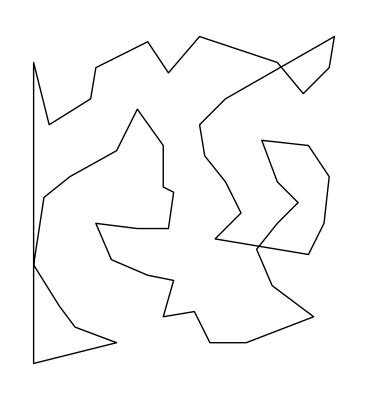

```mathematica
Graphics[Line[Pin[[VertexSolution]]]]
```

```mathematica
ArcLength[Line[Pin[[VertexSolution]]]]//N
```

481.519